# GRAVITAS Figure Reproductions

Luke Wriglesworth

Wolfram Institute

Here I reproduce some of the key results from Jonathan Gorard’s GRAVITAS papers, which provide a framework for working with General Relativity in the Wolfram Physics Project.

## Computational General Relativity in the Wolfram Language using Gravitas II: ADM Formalism and Numerical Relativity

https://arxiv.org/abs/2401.14209

### Figure 49, pg. 61

“A DiscreteHypersurfaceDecomposition object for a Schwarzschild geometry (representing, for instance, an uncharged, non-rotating black hole with numerical mass 1 in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) with spatial coordinate information assigned to the vertices.”

```mathematica
schwarzschildTensor = MetricTensor[{"Schwarzschild",1},{t,x,y,z}];
decomposition = DiscreteHypersurfaceDecomposition[schwarzschildTensor,{t,0,1},{x,-2,2},{y,-2,2},400,1.2];
schwarzschildTensor["MatrixRepresentation"]//MatrixForm
GraphPlot@decomposition[{"CoordinatizedCartesianGraphEvolutionColored",2}][[1]]
```

(-1+2/x | 0 | 0 | 0
0 | 1/(1-2/x) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

“ A DiscreteHypersurfaceDecomposition object for a Kerr geometry (representing, for instance, an uncharged, spinning black hole with numerical mass 1 and numerical angular momentum 1/3 in Boyer-Lindquist or oblate spheroidal coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) with spatial coordinate information assigned to
the vertices.”

```mathematica
kerrTensor = MetricTensor[{"Kerr",1,1/3},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[kerrTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
kerrTensor["MatrixRepresentation"]//MatrixForm
decomposition[{"CoordinatizedPolarGraphEvolutionColored",5}]
```

(-1+(2 r)/(r^2+Cos[θ]^2/9) | 0 | 0 | -(2 r Sin[θ]^2)/(3 (r^2+Cos[θ]^2/9))
0 | (r^2+Cos[θ]^2/9)/(1/9-2 r+r^2) | 0 | 0
0 | 0 | r^2+Cos[θ]^2/9 | 0
-(2 r Sin[θ]^2)/(3 (r^2+Cos[θ]^2/9)) | 0 | 0 | Sin[θ]^2 (1/9+r^2+(2 r Sin[θ]^2)/(9 (r^2+Cos[θ]^2/9))))

$Aborted

### Figure 50, pg. 62

“A DiscreteHypersurfaceDecomposition object for a Schwarzschild geometry (representing, for instance, an uncharged, non-rotating black hole with numerical mass 1 in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

```mathematica
solution = SolveVacuumADMEquations[ADMDecomposition[{"Schwarzschild",1},t,{r,θ,ϕ},√(1-(2*1)/r),{0,0,0}],0]
decomposition = DiscreteHypersurfaceDecomposition[solution["SpacetimeMetricTensor"],{t,0,24},{r,0,4},{θ,-Pi,Pi},500,1.1];

(*GraphPlot/@decomposition[{"PolarGraphEvolutionColored",3}]*)
```

VacuumADMSolution[…]

```mathematica
solution["SpacetimeMetricTensor"]["MatrixRepresentation"]//MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

“A DiscreteHypersurfaceDecomposition object for a Kerr geometry (representing, for instance, an uncharged, spinning black hole with numerical mass 1 and numerical angular momentum 1/3 in Boyer-Lindquist or oblate spheroidal coordinates (t, r, θ, ϕ) with t ∈ [0, 1], r ∈ [0, 4] and θ ∈ [−π, π]), with a resolution of 400 vertices and a discretization scale of 1.2, represented by the evolution of its spatial hypergraphs for five time steps from coordinate time t = 0 to coordinate time t = 1 (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

```mathematica
kerrTensor = MetricTensor[{"Kerr",1,1/3},{t,r,θ,ϕ}];
decomposition = DiscreteHypersurfaceDecomposition[kerrTensor,{t,0,1},{r,0,4},{θ,-Pi,Pi},400,1.2];
decomposition[{"PolarGraphEvolutionColored",5}]
```

## Figure 52, pg. 65

“The DiscreteHypersurfaceDecomposition object for a Brill-Lindquist geometry (representing, for instance, a pair of uncharged, non-rotating black holes, initially at rest, each of mass M in Schwarzschild or spherical polar coordinates (t, r, θ, ϕ) with the radial boundary R of the domain set to be comparable to the Schwarzschild radii of the black holes, i.e. R ∼ 2M ) with the 1 + log slicing condition and the minimal distortion coordinate conditions for the gauge, represented by the evolution of its spatial hypergraphs for six time steps from coordinate time t = 0M to coordinate time t = 24M (colored based on extrinsic curvature) without any vertex coordinate information assigned.”

```mathematica
adm = ADMDecomposition[{"BrillLindquist",5,10},t,{r,a1,a2},2,{0,0,0}]
graph = DiscreteHypersurfaceDecomposition[adm["SpacetimeMetricTensor"],{t,0,24},{r,0,20},{a1,-Pi,Pi},4000,1.2][{"CoordinatizedPolarGraphEvolutionColored",1}][[1]];
GraphPlot@graph
```

ADMDecomposition[…]

Computing christoffel symbols...

Computing riemann tensor...

Computing covariant riemann tensor...

Computing contravariant riemann tensor

Computing kretschmann scalar...

Discretizing region...

Generating points...

-Graphics-

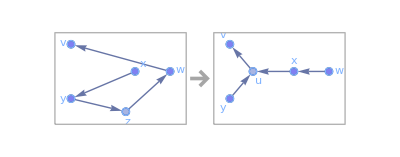

```mathematica
edges = graph // IndexGraph//EdgeList//Map[Apply[List]];
rule = {{x,y},{y,z},{z,w},{w,v}}->{{y,u},{u,v},{w,x},{x,u}};
RulePlot[
ResourceFunction["WolframModel"][{rule}]
,VertexLabels->"Name"
]
evolution = WolframModel[{rule},edges,<|"MaxEvents"->75|>]["StatesList"];
```

```mathematica
Get["/home/luke/Code/Gravitas/metric_tensor.m"];
Clear[metricTensorFunction]
timePoints=Range[Length[metricData]-1];
matrices=metricData;
interpolationFunctions=Table[Interpolation[Table[{timePoints[[t]],matrices[[t,i,j]]},{t,Length[timePoints]}],InterpolationOrder->1],{i,1,4},{j,1,4}];
metricTensorFunction[t_?NumericQ]:=Table[interpolationFunctions[[i,j]][t],{i,1,4},{j,1,4}];
metricTensorSymbolic[t_]:=Module[{time=t},Table[With[{i=i,j=j},Function[time,interpolationFunctions[[i,j]][time]]][time],{i,1,4},{j,1,4}]];
metricComponent[t_,μ_,ν_]:=metricTensorFunction[t][[μ+1,ν+1]];
g[t_]:=metricTensorSymbolic[t];
tensor = MetricTensor[g[t],{t,x,y,z},True,True]
decomposition = DiscreteHypersurfaceDecomposition[tensor,{t,0,10},{x,-5,5},{y,-Pi,Pi},2500,1.0]
```

MetricTensor[{{InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1, 16535}}, <>][t]}, «2», {InterpolatingFunction[{{1, 16535}}, <>][t], InterpolatingFunction[{{1, 16535}}, <>][t], InterpolatingFunction[«2»][t], InterpolatingFunction[{{1, 16535}}, <>][t]}}, «2», True]

DiscreteHypersurfaceDecomposition[MetricTensor[{{InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1., 16535.}}, <>][t], InterpolatingFunction[{{1, 16535}}, <>][t]}, {«4»}, {«4»}, {InterpolatingFunction[{{1, 16535}}, <>][t], Interp<<10>>ction[«2»][t], «1», InterpolatingFunction[{{1, 16535}}, <>][t]}}, «3»], «4», 1.]

```mathematica
GraphPlot/@decomposition[{"CoordinatizedCartesianGraphEvolutionColored",2}]
```

Computing riemann tensor...

Computing covariant riemann tensor...

Computing contravariant riemann tensor

Part::partd: Part specification contravariantRiemannTensor$207301⟦1,1,1,1⟧ is longer than depth of object.

Part::partd: Part specification contravariantRiemannTensor$207301⟦1,1,1,2⟧ is longer than depth of object.

Part::partd: Part specification contravariantRiemannTensor$207301⟦1,1,1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Needs["PacletTools`"];
PacletBuild["/home/luke/Code/Gravitas"];
PacletInstall["/home/luke/Code/Gravitas/build/Gravitas-1.0.0.paclet", ForceVersionInstall->True];
Needs["Gravitas`"]
```

PacletToolsGeneral::warning: Note: file 'Gravitas/metric_tensor.m' was not included in built paclet.